### @ 2 modes -

```mathematica
f[c0_,c1_]:=({{c0^2+2 c1^2}, {-1c1+2 c0 c1}})
F[P_]:=f[P[[1]],P[[2]]]
```

```mathematica
h[θ1_]:=(-θ1)


p0=({{0}, {0}});p1=({{0}, {1}});p2=({{-1+0(-1/4)}, {0}});p3=({{0}, {1}});p4=({{-5/4}, {0}});p5=({{0}, {9/8}});
p6=({{-9/6}, {0}});p7=({{0}, {31/24}});p8=({{-683/(48 8)}, {0}});p9=({{0}, {765/(64 8)}});p10=({{-8057/(384 10)}, {0}});
p11=({{0}, {22203/1280}})/10;p12=({{-189571/(6400 12)}, {0}});p13=({{0}, {1859683/76800}})/12;p14=({{-7793/192}, {0}})/14;
p15=({{0}, {7076011/215040}})/14;p16=({{-9831164969/180633600}, {0}})/16;p17=({{0}, {7039118181/160563200}})/16;
p18=({{-138320683367/1926758400}, {0}})/18;p19=({{0}, {399045367193/6936330240}})/18;p20=({{-7294219248473/78033715200}, {0}})/20;

P[θ1_]:=p0+p1 θ1+p2 θ1^2+p3 θ1^3+p4 θ1^4+
(p5 θ1^5+p6 θ1^6+p7 θ1^7+p8 θ1^8+p9 θ1^9+p10 θ1^10)+(p11 θ1^11+p12 θ1^12+p13 θ1^13+p14 θ1^14+p15 θ1^15+p16 θ1^16+p17 θ1^17+p18 θ1^18+p19 θ1^19+p20 θ1^20)

JacP[θ1_]=D[P[θ1],θ1];

xx=Simplify[Flatten[F[P[θ1]]- JacP[θ1]h[θ1]]];
Collect[xx,θ1]//MatrixForm;
xx//MatrixForm;
Collect[Series[xx,{θ1,0,20}]//Simplify,θ1]
```

{0,0}

```mathematica
Fim[c0_,c1_,λ_]:={Re[λ(c0^2+2 c1^2)],Im[λ(-1c1+2 c0 c1)],Re[λ(-1c1+2 c0 c1)]}
```

```mathematica
Fim[-1,1,I]
```

{0,-3,0}

```mathematica
Exp[I π/2]
```

ⅈ

```mathematica
I f[-1,1]
```

{{3 ⅈ},{-3 ⅈ}}

```mathematica
vectSize =.45;
rMax=.4;
gridMax=P[rMax][[2,1]];
λ=I;
vectSlice=SliceVectorPlot3D[Fim[c0,c1x+I c1y,λ],c1y==0,{c0,-gridMax,gridMax},{c1y,-gridMax,gridMax},{c1x,-gridMax,gridMax},VectorAspectRatio->1/4,VectorColorFunction->None,VectorSizes->vectSize]
vectSlice=%;
vectSlice2=SliceVectorPlot3D[Fim[c0,c1x+I c1y,λ],Re[P[c1x+c1y I][[1,1]]]-c0==0,{c0,-gridMax,gridMax},{c1y,-gridMax,gridMax},{c1x,-gridMax,gridMax},VectorAspectRatio->1/4,VectorColorFunction->(Darker[Darker[Brown]]&),VectorSizes->vectSize,RegionFunction->((#2^2 +#3^2<rMax^2)&),PlotStyle->{Orange,Opacity[.9]},VectorMarkers->{"Arrow3D","Middle",Black},AxesLabel->{"Re(a_0)","Im(a_1)","Re(a_1)"}]
vectSlice2=%;
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[vectSlice2,vectSlice]
```

-Graphics3D-

```mathematica
xxx=-Graphics3D-
```

```mathematica
xxx=-Graphics3D-
```

```mathematica
xxx=-Graphics3D-
```

-Graphics3D-

```mathematica
xxx=Show[vectSlice,vectSlice2]
```

-Graphics3D-

```mathematica
xxx=-Graphics3D-
```

-Graphics3D-

```mathematica
xxx
```

-Graphics3D-

# Real

```mathematica
P[0]
```

{{0},{0}}

```mathematica
Grid2Dθ=.5;
Grid2D=.5;
```

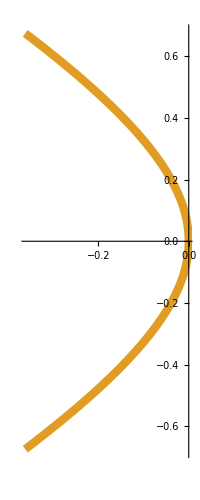

```mathematica
Ws=ParametricPlot[{{,},P[θ]},{θ,-Grid2Dθ,Grid2Dθ},PlotStyle->Thickness[.015]]
```

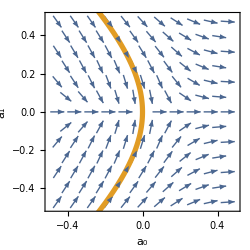

```mathematica
VectorPlot[{a0^2+2 a1^2,- a1+2 a0 a1},{a0,-Grid2D,Grid2D},{a1,-Grid2D,Grid2D},StreamColorFunction->None,VectorColorFunction->None,FrameLabel->{"a_0","a_1"},ImageSize->250,RotateLabel->False,VectorPoints->11];
realWs=Show[%,Ws]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\JonoS\Dropbox\etc\NLS\Real_initial_data\Final_Code\Mathematica

```mathematica
imRes=350;
```

```mathematica
Export["W2Mode_NLS.png",xxx,ImageResolution->imRes]
```

W2Mode_NLS.png

```mathematica
Export["realWs.png",realWs,ImageResolution->imRes]
```

realWs.png

```mathematica
realWs
```